## Setup

```mathematica
Get["FunKit`"]
```

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 0.1.1
Year: 2025
For more information and a brief introduction to the package, call FInfo[].
To run the testing suite, you can call  FTest[].

```mathematica
AddCorrelationFunction[PhiDot];
FSetUnorderedIndices[PhiDot,1];
FEx[FTerm[-PhiDot[{AnyField},{a}],GammaN[{AnyField},{-a}]],FTerm[1/2,Propagator[{AnyField,AnyField},{a,c}],FEx[FTerm[γ[{AnyField,AnyField},{-c,b}],Rdot[{AnyField,AnyField},{-a,-b}]],FTerm[FDOp[AnyField[c]],PhiDot[b],R[{AnyField,AnyField},{-a,-b}]]]]];
```

FEx[FTerm[-PhiDot[{AnyField},{a}],GammaN[{AnyField},{-a}]],FTerm[1/2,Propagator[{AnyField,AnyField},{a,c}],γ[{AnyField,AnyField},{-c,b}],Rdot[{AnyField,AnyField},{-a,-b}]],FTerm[1/2,Propagator[{AnyField,AnyField},{a,c}],FDOp[AnyField[c]],PhiDot[b],R[{AnyField,AnyField},{-a,-b}]]]

```mathematica
ShowObjects[]
```

Field
FMinus
GammaN
Phidot
Propagator
R
Rdot
S
SymmetryFactor
γ

```mathematica
Show
```

The following defines the scalar field theory and the truncation used. Here, the symmetric phase is assumed by setting Field->{} in the truncation. 
Warning: Setting Field->{ϕ} will give the results for the broken phase, but this will also greatly increase the number of terms in the four- and six-point functions, which may take a long time to compute.

```mathematica
fields= <|
"Commuting"-> {ϕ[p]},
"Grassmann"->{}
|>;
truncation=<|
GammaN->{{ϕ,ϕ},{ϕ,ϕ,ϕ,ϕ}},
Propagator->{{ϕ,ϕ}},
G->{{ϕ,ϕ}},
Rdot->{{ϕ,ϕ}},
S->{{ϕ,ϕ},{ϕ,ϕ,ϕ,ϕ}},
Field->{}
|>;
setup=<|
"FieldSpace"->fields,
"Truncation"->truncation
|>;
FSetGlobalSetup[setup];
```

If you would like to see what FunKit does underneath, you can set the debug level to values greater than 0. The numbers correspond to the following level of detail:
0: no info
1: basic information what is happening
2: in-depth what steps are being processed
3: the guts of the program
4: nested guts of the program
5: all details
6: information only needed for debugging

```mathematica
FSetDebugLevel[0];
```

## DSE

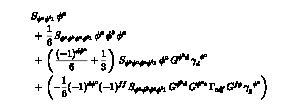

```mathematica
DSE=MakeDSE[ϕ[i1]]//FPrint;
```


-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

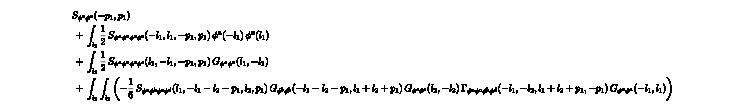

```mathematica
DSE2P=FTakeDerivatives[DSE,{ϕ[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

```mathematica
DSE4P=FTakeDerivatives[DSE,{ϕ[i2],ϕ[i3],ϕ[i4]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
DSE6P=FTakeDerivatives[DSE,{ϕ[i2],ϕ[i3],ϕ[i4],ϕ[i5],ϕ[i6]}]//FTruncate//FPlot//FRoute//FPrint;
```

$Aborted

## fRG

```mathematica
fRG2P=FTakeDerivatives[WetterichEquation,{ϕ[i1],ϕ[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-

-Graphics-

```mathematica
fRG4P=FTakeDerivatives[WetterichEquation,{ϕ[i1],ϕ[i2],ϕ[i3],ϕ[i4]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-

-Graphics-

```mathematica
fRG6P=FTakeDerivatives[WetterichEquation,{ϕ[i1],ϕ[i2],ϕ[i3],ϕ[i4],ϕ[i5],ϕ[i6]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-

-Graphics-

## 3PI

```mathematica
AddCorrelationFunction[G]
Γ3PI=MakeClassicalAction[setup]+FEx[FTerm[-1/2 Log[FTerm[G[{ϕ,ϕ},{i,-i}]]]]]+FEx[FTerm[S[{ϕ,ϕ},{i,j}],G[{ϕ,ϕ},{-i,-j}]]]
```

FEx[FTerm[-1/2 Log[FTerm[G[{ϕ,ϕ},{i,-i}]]]],FTerm[S[{ϕ,ϕ},{i,j}],G[{ϕ,ϕ},{-i,-j}]],FTerm[1/2,S[{ϕ,ϕ},{-i87,-i88}],ϕ[i87],ϕ[i88]],FTerm[1/24,S[{ϕ,ϕ,ϕ,ϕ},{-i89,-i90,-i91,-i92}],ϕ[i89],ϕ[i90],ϕ[i91],ϕ[i92]]]

```mathematica
FResolveDerivatives[setup,FTerm[FDOp[G[{ϕ,ϕ},{g,h}]]]**Γ3PI]
```

FEx[FTerm[-γ[{ϕ,ϕ},{-g,-h}]/(4 FTerm[G[{ϕ,ϕ},{i95,-i95}]])],FTerm[-γ[{ϕ,ϕ},{-h,-g}]/(4 FTerm[G[{ϕ,ϕ},{i96,-i96}]])],FTerm[S[{ϕ,ϕ},{-h,-g}]]]